## makes plots for SwarmControl.herokuapp.com Aaron T. Becker

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Load data, sort is, and do some analysis

```mathematica
SetDirectory[NotebookDirectory[]];
(*data = Import["show_results1.csv"];
data = Import["show_results0908.csv"];
data = Import["show_results0913.csv"];
data = Import["show_results0915.csv"];
data = Import["show_results1008.csv"];
data = Import["show_results1014.csv"];*)
data = Import["show_results0516.csv"];
ColNames = data⟦1⟧

(*remove bad data*)
data = Drop[data,1];
data =Select[data,#⟦1⟧!="" &]; (*some data was missing time and task name*)

TaskData=GatherBy[data,First];
FontSz = 16;
StringForm["Total experiments = ``",Length[data]]
StringForm["unique players = ``",Length[DeleteDuplicates[data,#1⟦3⟧==#2⟦3⟧&]]]
dates = Sort[data⟦;;,5⟧];
StringForm["Hours played = ``",Total[data⟦;;,4⟧]/(60*60)]
StringForm["Game Launched at = ``",dates⟦1⟧]
```

{Task,Mode,Participant,Run time,Created at,Robot count}

Total experiments = 19798

unique players = 5265

Hours played = 678.105

Game Launched at = 2013-08-07 19:21:22 UTC

## Plot for vary control forage

```mathematica
controlModesF
```

{{{{global,ZRk1DmfpZ7uRQ__wGFFDvg,98.85,2014-07-26 12:03:46 UTC,100,Mozilla/5.0 (X11; Linux x86_64; rv:31.0) Gecko/20100101 Firefox/31.0},1154,{global,FygG52e1zbXzc8nAEaPx4g,77.134,2016-05-17 13:52:19 UTC,100,Mozilla/5.0 (Windows NT 6.2; WOW64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/50.0.2661.102 Safari/537.36}},{1},{1}},1,1;;All}
 |  |  |  |

{1,3,2}

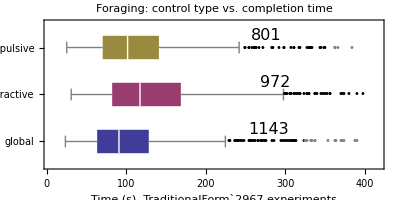

```mathematica
task = 6;
order = {1,3,2}
varyForage =GatherBy[Part[TaskData⟦task⟧,;;,2;;],First];
cf = Table[DeleteCases[varyForage⟦n,;;,3⟧,n_/;n>400] ,{n,1,Length[varyForage]}];
cleanForage={cf⟦1⟧,cf⟦3⟧,cf⟦2⟧};
clabel = varyForage⟦;;,1,1⟧;
controlModesF = {clabel⟦1⟧,clabel⟦3⟧,clabel⟦2⟧};
BoxWhiskerChart[cleanForage,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{controlModesF,Length/@cleanForage},{Axis,{.70,1}}],
AspectRatio->.5,
PlotLabel-> Style["Foraging: control type vs. completion time",FontSize->FontSz],
ChartStyle->1,ChartLabels->varyForage⟦;;,1,1⟧,BarOrigin->Left,LabelStyle->FontSz,FrameLabel->{StringForm[ "Time (s), `` experiments",Length[TaskData⟦task⟧]]}]
Export["../pictures/pdf/ResVaryForage.pdf",%];
```

### ANOVA Analysis (null hypothesis: the control type does not matter)

```mathematica
Needs["ANOVA`"]
ANOVA[Transpose[{Flatten[varyForage⟦;;,;;,1⟧],Flatten[varyForage⟦;;,;;,3⟧]}]]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 2 | 547183. | 273592. | 12.785 | 2.9606×10^-6
Error | 2964 | 6.34281×10^7 | 21399.5 |  | 
Total | 2966 | 6.39753×10^7 |  |  | ,CellMeans→All | 128.605
Model[attractive] | 147.469
Model[global] | 117.025
Model[repulsive] | 121.882}

## Plot for Robot Positioning

A box - and - whisker plot (sometimes called simply a box plot) is a histogram - like method of displaying data, invented by J.Tukey.To create a box - and - whisker plot, draw a box with ends at the quartiles Q_ 1 and Q_ 3. Draw the statistical median M as a horizontal line in the box.Now extend the "whiskers" to the farthest points that are not outliers (i.e., that are within 3/2 times the interquartile range of Q_ 1 and Q_ 3).Then, for every point more than 3/2 times the interquartile range from the end of a box, draw a dot.If two dots have the same value, draw them side by side (Gonick and Smith 1993, p.21).Box - and - whisker plots are implemented as BoxWhiskerPlot[data] in the Mathematica package StatisticalPlots`.
http://mathworld.wolfram.com/Box-and-WhiskerPlot.html

```mathematica
Needs["ANOVA`"]
```

```mathematica
ANOVA[cleanPos]
```

ANOVA::arg1: The 1st argument has unequal columns or rows.

ANOVA[{{1.102,1.103,1.143,1.157,1.18,1.202,1.205,1.22,1.22,1.221,1.222,1.222,1.222,1.224,1.225,1.225,1.226,1.226,1.227,1.227,1.227,1.228,1.229,1.229,1.231,1.232,1.232,1.233,1.233,1.234,1.234,1.235,1.235,1.236,1.236,1.237,1.238,1.239,1.239,1.239,1.239,1.239,1.24,1.24,1.24,1.241,1.241,1.241,1.241,1.241,1.242,1.242,1.242,1.242,1.242,1.243,1.244,1.244,1.244,1.245,1.245,1.245,1.246,1.246,1.247,1.248,1.248,1.248,1.25,1.25,1.25,1.251,1.251,1.251,1.252,1.252,1.252,1.253,1.253,1.254,1.254,1.254,1.255,1.255,1.258,1.258,1.258,1.258,1.258,1.259,1.259,1.259,1.26,1.26,1.26,1.261,1.261,1.262,1.262,1.262,1.263,1.264,1.265,1.265,1.266,1.266,1.267,1.268,1.268,1.27,1.27,1.27,1.271,1.272,1.272,1.272,1.273,1.273,1.275,1.275,1.276,1.277,1.277,1.278,1.279,1.282,1.283,1.283,1.288,1.288,1.29,1.291,1.291,1.291,1.292,1.293,1.294,1.295,1.295,1.295,1.296,1.297,1.297,1.298,1.299,1.299,1.299,1.303,1.305,1.305,1.307,1.307,1.307,1.308,1.309,1.31,1.311,1.312,1.313,1.314,1.315,1.316,1.317,1.319,1.322,1.323,1.325,1.326,1.331,1.334,1.339,1.341,1.344,1.35,1.351,1.352,1.355,1.361,1.366,1.37,1.372,1.375,1.379,1.379,1.383,1.383,1.386,1.387,1.387,1.389,1.392,1.393,1.393,1.393,1.394,1.395,1.4,1.401,1.407,1.409,1.413,1.417,1.419,1.421,1.424,1.425,1.425,1.428,1.443,1.443,1.445,1.457,1.462,1.474,1.477,1.478,1.486,1.489,1.502,1.508,1.51,1.522,1.527,1.527,1.527,1.53,1.548,1.551,1.558,1.569,1.571,1.573,1.584,1.584,1.586,1.594,1.606,1.606,1.608,1.617,1.621,1.622,1.628,1.63,1.636,1.637,1.638,1.642,1.649,1.651,1.655,1.662,1.665,1.668,1.67,1.67,1.673,1.679,1.686,1.688,1.69,1.692,1.71,1.712,1.714,1.72,1.722,1.724,1.724,1.728,1.729,1.731,1.733,1.735,1.738,1.738,1.739,1.741,1.743,1.747,1.757,1.757,1.757,1.759,1.76,1.764,1.768,1.768,1.772,1.774,1.779,1.78,1.79,1.792,1.792,1.795,1.795,1.797,1.802,1.806,1.807,1.812,1.813,1.816,1.817,1.82,1.821,1.825,1.834,1.837,1.839,1.841,1.845,1.846,1.847,1.848,1.852,1.854,1.854,1.856,1.867,1.867,1.867,1.869,1.872,1.876,1.877,1.886,1.894,1.898,1.9,1.911,1.918,1.918,1.924,1.925,1.928,1.929,1.933,1.935,1.943,1.943,1.951,1.953,1.954,1.956,1.963,1.968,1.969,1.97,1.97,1.971,1.971,1.973,1.985,1.986,1.986,1.993,1.994,1.995,2.006,2.007,2.007,2.007,2.01,2.011,2.014,2.017,2.022,2.023,2.025,2.028,2.029,2.036,2.037,2.041,2.052,2.052,2.057,2.058,2.059,2.059,2.059,2.061,2.065,2.065,2.07,2.071,2.072,2.073,2.073,2.075,2.08,2.081,2.082,2.085,2.086,2.089,2.091,2.095,2.096,2.096,2.097,2.1,2.101,2.102,2.104,2.104,2.107,2.107,2.11,2.122,2.131,2.131,2.143,2.144,2.155,2.156,2.161,2.167,2.171,2.173,2.175,2.176,2.182,2.186,2.188,2.19,2.192,2.192,2.193,2.194,2.198,2.199,2.207,2.21,2.211,2.212,2.226,2.229,2.231,2.236,2.239,2.239,2.239,2.253,2.259,2.26,2.263,2.264,2.267,2.269,2.272,2.273,2.278,2.282,2.283,2.292,2.301,2.311,2.312,2.321,2.321,2.321,2.322,2.323,2.323,2.324,2.325,2.327,2.33,2.336,2.336,2.341,2.346,2.347,2.349,2.361,2.37,2.386,2.386,2.393,2.398,2.398,2.401,2.401,2.406,2.409,2.426,2.43,2.444,2.451,2.453,2.456,2.458,2.461,2.467,2.47,2.477,2.483,2.491,2.493,2.502,2.508,2.515,2.517,2.52,2.52,2.521,2.527,2.53,2.534,2.535,2.536,2.539,2.55,2.555,2.56,2.569,2.572,2.572,2.578,2.585,2.588,2.591,2.594,2.594,2.597,2.598,2.608,2.62,2.622,2.623,2.632,2.633,2.635,2.639,2.644,2.646,2.649,2.652,2.662,2.662,2.67,2.671,2.684,2.693,2.708,2.71,2.711,2.712,2.725,2.731,2.742,2.744,2.745,2.752,2.757,2.768,2.774,2.774,2.778,2.778,2.78,2.785,2.79,2.794,2.798,2.801,2.814,2.823,2.829,2.833,2.837,2.839,2.84,2.851,2.864,2.87,2.872,2.88,2.882,2.885,2.905,2.914,2.916,2.919,2.922,2.923,2.939,2.939,2.951,2.957,2.957,2.958,2.982,2.983,2.989,2.991,2.994,2.997,3.006,3.011,3.012,3.025,3.029,3.035,3.036,3.038,3.04,3.043,3.052,3.052,3.055,3.057,3.06,3.061,3.067,3.081,3.083,3.091,3.101,3.105,3.109,3.11,3.114,3.117,3.117,3.121,3.125,3.129,3.143,3.147,3.15,3.159,3.164,3.166,3.17,3.172,3.184,3.187,3.19,3.192,3.207,3.22,3.232,3.234,3.236,3.239,3.241,3.243,3.245,3.259,3.264,3.278,3.294,3.294,3.294,3.299,3.299,3.299,3.318,3.324,3.337,3.344,3.345,3.367,3.374,3.378,3.385,3.389,3.415,3.432,3.442,3.45,3.451,3.456,3.458,3.461,3.464,3.464,3.466,3.467,3.47,3.473,3.476,3.477,3.483,3.488,3.501,3.501,3.505,3.512,3.529,3.54,3.556,3.573,3.585,3.593,3.624,3.638,3.656,3.672,3.687,3.695,3.708,3.715,3.719,3.723,3.741,3.754,3.759,3.762,3.767,3.773,3.803,3.803,3.829,3.835,3.836,3.86,3.866,3.872,3.884,3.888,3.893,3.895,3.899,3.907,3.908,3.916,3.945,3.95,3.963,3.97,3.972,3.976,4.001,4.057,4.064,4.081,4.083,4.127,4.128,4.156,4.175,4.209,4.215,4.221,4.226,4.227,4.236,4.239,4.251,4.269,4.288,4.29,4.291,4.291,4.311,4.332,4.349,4.422,4.433,4.482,4.505,4.526,4.527,4.528,4.528,4.534,4.561,4.578,4.592,4.631,4.685,4.733,4.789,4.804,4.855,4.868,4.93,4.931,4.932,4.959,4.961,4.965,4.975,4.981,4.996,5.03,5.067,5.116,5.117,5.118,5.132,5.151,5.162,5.219,5.244,5.259,5.262,5.293,5.317,5.323,5.349,5.379,5.386,5.405,5.442,5.444,5.477,5.51,5.518,5.522,5.526,5.56,5.604,5.61,5.638,5.676,5.678,5.754,5.774,5.787,5.804,5.816,5.831,5.878,6.09,6.094,6.11,6.118,6.22,6.299,6.355,6.39,6.493,6.509,6.541,6.552,6.589,6.597,6.624,6.656,6.701,6.867,6.91,7.083,7.114,7.156,7.191,7.255,7.263,7.27,7.464,7.471,7.474,7.546,7.587,7.669,7.669,7.852,8.031,8.06,8.179,8.211,8.237,8.246,8.31,8.391,8.44,8.513,8.515,8.664,8.71,8.788,8.88,8.943,8.996,9.019,9.099,9.244,9.301,9.402,9.413,9.45,9.614,9.844,9.936,10.196,10.317,10.419,10.455,10.506,10.562,10.821,11.173,11.217,11.311,11.465,11.5,11.689,12.069,13.33,13.355,13.663,14.327,15.163,15.566,15.752,16.521,17.292,20.463,21.288,22.451,25.11,28.346,30.048,46.558},{2.565,2.915,2.924,3.21,3.277,3.324,3.338,3.352,3.463,3.481,3.541,3.544,3.557,3.577,3.62,3.625,3.656,3.657,3.709,3.775,3.927,4.014,4.016,4.05,4.064,4.067,4.117,4.121,4.127,4.141,4.147,4.148,4.172,4.203,4.219,4.228,4.287,4.288,4.291,4.37,4.377,4.378,4.387,4.395,4.412,4.426,4.436,4.444,4.451,4.46,4.466,4.517,4.565,4.586,4.595,4.606,4.636,4.675,4.675,4.784,4.785,4.806,4.81,4.817,4.82,4.822,4.844,4.856,4.865,4.877,4.879,4.894,4.908,4.909,4.933,4.957,4.972,4.99,5.002,5.04,5.057,5.073,5.136,5.143,5.163,5.168,5.196,5.223,5.271,5.279,5.31,5.322,5.325,5.326,5.329,5.337,5.348,5.368,5.369,5.376,5.39,5.395,5.422,5.428,5.468,5.486,5.491,5.501,5.522,5.524,5.533,5.539,5.559,5.572,5.596,5.601,5.621,5.624,5.63,5.657,5.68,5.681,5.69,5.697,5.705,5.715,5.738,5.739,5.742,5.747,5.754,5.79,5.798,5.811,5.831,5.844,5.854,5.856,5.873,5.913,5.92,5.929,5.932,5.943,5.953,5.953,5.957,5.958,5.975,6.003,6.021,6.033,6.093,6.111,6.121,6.123,6.145,6.158,6.206,6.229,6.23,6.244,6.258,6.258,6.277,6.283,6.305,6.306,6.324,6.377,6.395,6.403,6.404,6.409,6.456,6.495,6.542,6.552,6.566,6.572,6.581,6.6,6.633,6.648,6.663,6.685,6.691,6.746,6.757,6.758,6.774,6.823,6.87,6.893,6.897,6.95,6.98,6.997,7.013,7.093,7.1,7.111,7.156,7.159,7.164,7.188,7.204,7.205,7.214,7.234,7.24,7.25,7.279,7.299,7.331,7.366,7.404,7.409,7.421,7.424,7.442,7.464,7.504,7.51,7.523,7.555,7.58,7.606,7.611,7.636,7.647,7.671,7.68,7.685,7.701,7.719,7.729,7.734,7.737,7.742,7.781,7.806,7.806,7.81,7.813,7.847,7.849,7.865,7.874,7.875,7.883,8.011,8.04,8.049,8.12,8.156,8.162,8.164,8.187,8.207,8.211,8.218,8.236,8.237,8.239,8.244,8.318,8.32,8.334,8.368,8.469,8.508,8.512,8.541,8.558,8.558,8.577,8.592,8.593,8.659,8.659,8.69,8.717,8.722,8.727,8.735,8.74,8.744,8.788,8.79,8.803,8.805,8.832,8.848,8.863,8.88,8.906,8.936,8.947,8.972,8.996,9.055,9.069,9.079,9.113,9.151,9.168,9.205,9.207,9.223,9.226,9.228,9.255,9.288,9.288,9.29,9.29,9.294,9.307,9.328,9.332,9.345,9.348,9.355,9.36,9.368,9.38,9.393,9.456,9.471,9.513,9.53,9.532,9.558,9.562,9.589,9.601,9.685,9.711,9.759,9.763,9.768,9.771,9.834,9.852,9.854,9.857,9.858,9.892,9.924,9.927,9.944,9.98,9.986,10,10.064,10.073,10.078,10.108,10.112,10.198,10.211,10.256,10.259,10.268,10.291,10.309,10.4,10.405,10.458,10.494,10.494,10.529,10.544,10.554,10.559,10.57,10.595,10.598,10.614,10.65,10.653,10.664,10.69,10.715,10.719,10.738,10.818,10.9,10.925,10.927,11.02,11.027,11.027,11.031,11.036,11.057,11.058,11.08,11.15,11.201,11.246,11.256,11.264,11.275,11.321,11.339,11.361,11.402,11.434,11.45,11.456,11.587,11.588,11.603,11.606,11.645,11.663,11.667,11.672,11.733,11.891,11.938,11.952,11.964,11.989,12.032,12.037,12.04,12.1,12.106,12.114,12.126,12.147,12.166,12.17,12.188,12.228,12.265,12.324,12.39,12.403,12.413,12.416,12.419,12.514,12.537,12.55,12.568,12.58,12.584,12.764,12.816,12.827,12.839,12.841,12.848,12.849,12.872,12.879,12.969,12.988,13.01,13.046,13.096,13.191,13.212,13.223,13.231,13.236,13.25,13.255,13.384,13.395,13.417,13.42,13.452,13.459,13.495,13.497,13.528,13.53,13.581,13.595,13.604,13.635,13.637,13.645,13.668,13.676,13.698,13.718,13.72,13.745,13.755,13.774,13.854,13.879,13.917,13.954,14.02,14.045,14.088,14.104,14.145,14.188,14.212,14.231,14.312,14.319,14.345,14.37,14.411,14.413,14.548,14.627,14.665,14.671,14.736,14.744,14.858,14.875,14.887,14.912,14.995,15.098,15.224,15.238,15.347,15.367,15.379,15.422,15.473,15.475,15.478,15.487,15.505,15.532,15.635,15.643,15.645,15.658,15.678,15.683,15.874,15.878,15.922,15.987,16.034,16.076,16.129,16.172,16.179,16.266,16.353,16.373,16.411,16.421,16.425,16.515,16.575,16.641,16.729,16.797,16.933,16.96,16.971,17.029,17.082,17.143,17.156,17.188,17.211,17.248,17.262,17.326,17.422,17.557,17.563,17.89,17.944,17.992,18.05,18.082,18.212,18.235,18.281,18.514,18.543,18.62,18.689,18.715,18.735,18.815,18.925,19.003,19.025,19.05,19.105,19.292,19.301,19.31,19.343,19.452,19.551,19.755,19.763,19.777,19.857,19.878,19.992,20.174,20.217,20.248,20.264,20.311,20.549,20.572,20.575,20.737,20.751,20.903,20.972,20.973,21.018,21.093,21.182,21.229,21.272,21.299,21.305,21.32,21.362,21.527,21.939,21.968,22.247,22.39,22.473,22.513,22.576,22.605,22.643,22.834,22.865,22.979,23.257,23.385,23.405,23.486,23.594,23.828,23.858,24.056,24.185,24.284,24.456,24.484,24.905,25.118,25.138,25.191,25.255,25.403,25.521,25.555,25.953,25.974,26.045,26.169,26.297,26.342,26.389,26.69,27.045,27.09,27.424,27.452,27.565,27.858,28.027,28.346,28.469,28.674,28.846,29.584,29.733,30.105,30.302,30.379,30.607,31.376,31.58,31.828,32.631,34.279,34.56,34.833,34.883,35.459,35.464,35.482,35.56,35.571,35.578,35.808,36.194,36.785,37.452,37.594,38.521,38.528,39.404,39.699,39.777,40.474,41.097,43.123,43.302,43.441,45.562,45.963,46.028,46.066,46.319,46.402,46.829,50.171,50.487,58.516,64.228,69.013,69.423,71.487,77.087,84.323,85.734,96.473},{3.244,3.291,3.385,3.519,3.579,3.582,3.629,3.642,3.688,3.779,3.853,3.966,3.967,3.991,4.039,4.068,4.146,4.211,4.229,4.24,4.273,4.285,4.305,4.359,4.363,4.523,4.548,4.56,4.563,4.566,4.649,4.688,4.705,4.727,4.727,4.838,4.855,4.886,4.899,4.912,4.926,4.95,4.968,4.976,4.978,5.017,5.02,5.058,5.065,5.072,5.086,5.101,5.126,5.149,5.153,5.171,5.171,5.174,5.181,5.193,5.198,5.201,5.222,5.239,5.292,5.298,5.314,5.322,5.337,5.343,5.35,5.359,5.374,5.376,5.42,5.426,5.427,5.433,5.437,5.447,5.453,5.456,5.461,5.466,5.477,5.483,5.485,5.492,5.498,5.499,5.532,5.539,5.542,5.569,5.594,5.605,5.65,5.687,5.694,5.709,5.724,5.725,5.739,5.754,5.761,5.778,5.809,5.815,5.817,5.819,5.823,5.86,5.942,5.977,5.986,5.99,5.993,6.003,6.008,6.048,6.061,6.062,6.069,6.096,6.104,6.114,6.123,6.14,6.145,6.174,6.183,6.19,6.198,6.208,6.224,6.229,6.24,6.249,6.252,6.274,6.275,6.293,6.304,6.304,6.316,6.318,6.324,6.358,6.371,6.371,6.412,6.432,6.452,6.493,6.497,6.504,6.504,6.515,6.527,6.534,6.565,6.616,6.619,6.628,6.632,6.635,6.645,6.672,6.683,6.69,6.693,6.694,6.728,6.735,6.74,6.741,6.743,6.75,6.771,6.805,6.812,6.842,6.851,6.851,6.864,6.905,6.924,6.924,6.943,6.946,6.947,6.957,6.985,6.985,7.016,7.037,7.044,7.05,7.061,7.073,7.079,7.1,7.109,7.131,7.144,7.156,7.156,7.16,7.169,7.172,7.183,7.184,7.193,7.195,7.204,7.204,7.204,7.205,7.216,7.224,7.227,7.239,7.24,7.248,7.275,7.288,7.294,7.295,7.295,7.304,7.316,7.318,7.328,7.329,7.341,7.345,7.357,7.358,7.366,7.406,7.407,7.415,7.421,7.444,7.46,7.474,7.487,7.499,7.518,7.568,7.621,7.625,7.627,7.669,7.676,7.678,7.694,7.708,7.711,7.715,7.767,7.786,7.812,7.823,7.828,7.842,7.869,7.87,7.917,7.934,7.936,7.936,8.025,8.042,8.042,8.064,8.064,8.135,8.138,8.144,8.145,8.153,8.196,8.23,8.272,8.292,8.311,8.315,8.318,8.336,8.341,8.376,8.388,8.426,8.454,8.468,8.487,8.494,8.503,8.505,8.556,8.574,8.607,8.61,8.648,8.658,8.663,8.684,8.69,8.707,8.717,8.718,8.723,8.725,8.727,8.791,8.794,8.795,8.799,8.811,8.838,8.89,8.896,8.917,8.92,8.925,8.955,8.957,8.974,8.976,9.006,9.036,9.038,9.043,9.072,9.159,9.164,9.182,9.198,9.205,9.227,9.228,9.231,9.231,9.238,9.244,9.279,9.343,9.354,9.415,9.44,9.478,9.494,9.501,9.555,9.556,9.559,9.579,9.579,9.583,9.606,9.622,9.629,9.683,9.683,9.759,9.771,9.788,9.797,9.814,9.845,9.876,9.881,9.895,9.911,9.912,9.923,9.924,9.928,9.943,10.014,10.032,10.037,10.037,10.046,10.06,10.103,10.111,10.114,10.137,10.167,10.185,10.223,10.224,10.225,10.228,10.233,10.244,10.262,10.263,10.277,10.322,10.375,10.377,10.384,10.403,10.434,10.445,10.476,10.482,10.519,10.568,10.652,10.657,10.697,10.722,10.73,10.756,10.794,10.803,10.831,10.912,10.937,10.938,10.959,11.067,11.072,11.097,11.112,11.117,11.202,11.208,11.225,11.26,11.271,11.304,11.357,11.374,11.594,11.649,11.658,11.675,11.693,11.747,11.752,11.76,11.787,11.814,11.839,11.846,11.874,11.92,11.923,11.939,11.968,11.979,11.994,12.011,12.086,12.087,12.119,12.128,12.176,12.188,12.193,12.218,12.25,12.278,12.284,12.342,12.36,12.373,12.39,12.404,12.452,12.452,12.486,12.523,12.545,12.583,12.596,12.631,12.645,12.659,12.664,12.676,12.718,12.769,12.769,12.805,12.855,12.879,12.88,12.918,12.939,12.966,12.996,13.012,13.018,13.024,13.057,13.059,13.092,13.177,13.203,13.224,13.249,13.26,13.294,13.354,13.371,13.455,13.501,13.549,13.593,13.644,13.658,13.665,13.685,13.687,13.811,13.856,13.897,13.935,13.976,14.028,14.038,14.238,14.247,14.32,14.332,14.334,14.341,14.353,14.388,14.41,14.468,14.485,14.499,14.86,14.89,14.895,14.899,14.911,14.943,15.033,15.072,15.178,15.181,15.201,15.21,15.228,15.238,15.256,15.275,15.331,15.338,15.344,15.386,15.409,15.545,15.603,15.635,15.639,15.671,15.786,15.802,15.819,15.834,15.843,15.89,15.955,16.036,16.171,16.178,16.231,16.259,16.272,16.379,16.398,16.448,16.449,16.477,16.5,16.508,16.509,16.563,16.564,16.583,16.588,16.616,16.668,16.695,16.733,16.757,16.769,17.019,17.084,17.184,17.241,17.255,17.257,17.357,17.375,17.461,17.463,17.478,17.492,17.516,17.556,17.626,17.736,17.912,18.062,18.238,18.458,18.523,18.534,18.554,18.662,18.681,18.898,18.961,19.007,19.009,19.018,19.171,19.296,19.356,19.36,19.457,19.483,19.608,19.612,19.715,19.743,19.947,19.954,19.998,20.051,20.103,20.106,20.182,20.354,20.516,20.522,20.586,20.64,20.669,20.69,21.063,21.076,21.185,21.36,21.566,21.594,21.788,21.886,21.928,22.818,22.855,23.164,23.574,23.827,23.858,23.94,24.068,24.165,24.3,24.565,24.687,24.871,24.91,24.937,24.962,25.051,25.373,25.493,25.692,25.845,26.088,26.282,26.54,26.678,26.694,26.842,27.506,27.518,27.88,27.948,28.127,28.465,28.682,28.865,28.905,29.306,29.336,29.585,29.845,30.484,30.549,31.297,31.312,31.428,32.25,32.298,32.428,32.464,32.506,32.735,32.742,32.849,33.074,33.143,33.313,33.765,33.841,33.857,34.134,34.937,35.227,35.494,36.614,36.928,37.433,39.42,39.688,39.904,40.56,40.96,41.827,41.984,43.007,44.353,46.003,47.087,47.974,48.603,54.072,54.867,62.01,62.898,63.066,66.458,66.6,70.721,70.869,71.214,72.837,78.311,79.056,81.378,91.728,103.178,104.872,105.451,110.301,128.783,136.241,148.791},{3.345,3.415,3.901,3.932,4.227,4.301,4.305,4.331,4.419,4.425,4.448,4.458,4.475,4.588,4.592,4.634,4.659,4.711,4.73,4.771,4.807,4.838,4.856,4.857,4.886,4.895,4.897,4.92,4.928,5.009,5.026,5.042,5.051,5.052,5.137,5.138,5.266,5.268,5.282,5.315,5.352,5.359,5.366,5.37,5.381,5.404,5.425,5.439,5.507,5.538,5.542,5.562,5.59,5.595,5.617,5.617,5.655,5.751,5.756,5.812,5.835,5.853,5.854,5.888,5.888,5.928,5.975,5.981,6.001,6.009,6.01,6.02,6.037,6.06,6.072,6.078,6.092,6.122,6.182,6.22,6.224,6.234,6.239,6.241,6.294,6.311,6.317,6.354,6.386,6.409,6.422,6.44,6.443,6.462,6.487,6.506,6.538,6.543,6.551,6.598,6.63,6.636,6.707,6.711,6.72,6.723,6.774,6.791,6.812,6.823,6.854,6.854,6.868,6.883,6.884,6.906,6.922,6.959,7.01,7.143,7.157,7.175,7.191,7.204,7.207,7.296,7.313,7.325,7.335,7.341,7.376,7.386,7.391,7.4,7.406,7.418,7.461,7.468,7.497,7.501,7.541,7.578,7.636,7.644,7.655,7.666,7.685,7.692,7.721,7.722,7.729,7.768,7.8,7.808,7.81,7.818,7.824,7.828,7.851,7.854,7.859,7.865,7.87,7.909,7.918,7.919,7.929,7.945,7.949,7.973,8.002,8.054,8.084,8.117,8.161,8.168,8.187,8.215,8.219,8.236,8.276,8.328,8.338,8.338,8.356,8.373,8.404,8.429,8.442,8.462,8.496,8.532,8.54,8.553,8.561,8.672,8.682,8.691,8.71,8.713,8.718,8.743,8.794,8.814,8.823,8.831,8.838,8.931,8.935,8.948,8.967,8.967,9.022,9.035,9.046,9.079,9.086,9.09,9.116,9.15,9.152,9.201,9.207,9.237,9.289,9.299,9.309,9.359,9.36,9.379,9.382,9.384,9.439,9.546,9.585,9.598,9.601,9.611,9.676,9.752,9.762,9.768,9.771,9.8,9.834,9.867,9.88,9.884,9.885,9.886,9.887,9.92,9.973,10.014,10.017,10.082,10.083,10.088,10.132,10.141,10.155,10.176,10.18,10.206,10.207,10.234,10.253,10.255,10.258,10.278,10.286,10.349,10.436,10.464,10.485,10.491,10.547,10.573,10.591,10.594,10.614,10.622,10.661,10.681,10.75,10.794,10.812,10.863,10.884,11.024,11.026,11.063,11.064,11.086,11.144,11.146,11.15,11.195,11.209,11.237,11.265,11.292,11.299,11.317,11.384,11.41,11.498,11.617,11.624,11.676,11.719,11.733,11.736,11.778,11.908,11.946,11.961,11.997,12.005,12.023,12.055,12.088,12.104,12.198,12.207,12.236,12.263,12.273,12.277,12.279,12.287,12.31,12.335,12.398,12.451,12.451,12.468,12.511,12.532,12.57,12.572,12.627,12.641,12.671,12.719,12.746,12.748,12.775,12.802,12.822,12.834,12.836,12.867,12.948,12.989,13.048,13.05,13.07,13.174,13.175,13.179,13.225,13.227,13.268,13.275,13.291,13.295,13.309,13.358,13.397,13.491,13.531,13.536,13.639,13.645,13.662,13.674,13.703,13.719,13.734,13.749,13.75,13.794,13.833,13.84,13.871,13.874,13.908,13.948,13.957,14.067,14.07,14.09,14.185,14.187,14.242,14.375,14.412,14.486,14.513,14.547,14.591,14.631,14.645,14.652,14.674,14.734,14.918,15.017,15.106,15.208,15.225,15.357,15.515,15.598,15.655,15.674,15.687,15.694,15.717,15.78,15.826,15.899,15.966,15.969,16.025,16.117,16.158,16.181,16.225,16.285,16.405,16.425,16.453,16.461,16.475,16.537,16.562,16.624,16.65,16.688,16.694,16.699,16.751,16.775,16.842,16.842,17.066,17.078,17.132,17.157,17.169,17.197,17.283,17.313,17.356,17.363,17.47,17.48,17.673,17.684,17.684,17.71,17.728,17.739,17.75,17.835,17.865,17.937,17.941,18.074,18.155,18.164,18.333,18.337,18.385,18.398,18.401,18.436,18.463,18.562,18.593,18.641,18.668,18.688,19.068,19.175,19.244,19.31,19.423,19.624,19.659,19.895,19.896,19.897,19.984,20.139,20.24,20.282,20.291,20.328,20.356,20.453,20.464,20.478,20.479,20.524,20.527,20.649,20.755,20.772,20.776,20.879,21.009,21.039,21.074,21.095,21.102,21.165,21.179,21.22,21.227,21.317,21.372,21.439,21.444,21.536,21.766,21.775,21.819,21.862,21.922,21.956,21.961,21.964,22.017,22.028,22.054,22.058,22.174,22.204,22.25,22.285,22.336,22.453,22.567,22.621,22.655,22.75,22.781,22.928,23.022,23.159,23.275,23.439,23.625,23.627,23.692,23.826,24.057,24.316,24.357,24.418,24.56,24.616,24.998,25.079,25.085,25.11,25.134,25.211,25.226,25.256,25.752,26.055,26.224,26.231,26.376,26.708,26.817,26.975,27.214,27.245,27.329,27.507,27.837,27.959,28.119,28.277,28.71,28.767,28.915,29.143,29.208,29.399,29.483,29.792,29.992,30.012,30.407,30.56,30.643,30.797,30.851,30.998,31.047,31.544,32.461,32.469,33.304,33.41,33.6,34.138,34.333,34.624,34.802,34.958,35.001,36.17,36.32,36.682,36.685,37.528,37.583,37.81,38.111,38.263,38.362,38.424,38.854,38.864,39.012,39.253,39.327,40.055,40.111,40.429,40.553,40.922,41.281,41.304,41.411,41.923,42.663,43.453,44.797,44.871,45.565,45.796,47.21,47.6,47.914,49.258,49.662,49.974,50.971,51.248,51.688,51.94,52.873,55.881,56.298,57.044,58.568,59.227,59.501,60.089,64.088,66.119,69.389,71.57,76.493,89.217,91.082,97.27,98.703,100.932,107.385,112.145,117.946,131.652,140.6,143.12,168.24},{11.133,11.892,12.352,13.19,14.364,14.644,15.033,15.092,15.183,15.727,16.534,16.782,16.989,17.565,17.687,17.722,17.878,18.606,18.625,18.866,18.979,19.209,19.281,19.572,20.449,21.22,21.417,21.653,21.906,22.371,22.722,23.561,23.601,23.613,24.505,24.624,25.106,25.308,25.353,25.383,25.406,25.498,26.433,26.557,27.003,27.096,27.66,27.695,28.139,28.676,28.746,28.802,29.054,29.329,29.38,29.524,29.524,29.572,29.673,29.819,29.984,30.214,30.314,30.486,30.505,30.578,30.869,30.948,31.081,31.214,32.154,32.337,32.356,32.566,32.681,32.742,32.761,32.957,32.982,33.207,33.365,33.596,33.732,33.943,34.249,34.601,34.621,35.377,35.379,35.454,35.773,35.798,35.836,35.846,35.909,36.08,36.201,36.262,36.42,36.605,36.761,36.821,36.937,37.036,37.041,37.225,37.456,38.08,38.089,38.186,38.294,38.615,38.618,38.859,39.146,39.377,39.515,39.803,39.813,39.9,40.511,40.553,40.646,40.794,40.999,41.153,41.272,41.473,41.576,41.689,41.802,41.893,41.939,42.039,42.453,42.83,42.927,43.063,43.303,43.447,43.546,43.558,43.724,44.025,44.086,44.171,44.185,44.261,44.348,44.351,44.383,44.576,44.764,44.846,45.119,45.197,45.314,45.381,45.42,45.625,45.673,46.109,46.258,46.431,46.464,46.638,46.656,46.674,46.799,46.932,47.534,47.594,47.994,48.01,48.21,48.358,48.396,48.44,48.442,48.7,48.844,48.858,48.867,49.089,49.637,49.765,49.828,49.971,50.408,50.64,50.684,51.275,51.315,51.898,52.362,52.589,52.847,52.958,53.156,53.741,54.126,54.323,54.377,54.414,54.417,54.469,54.685,54.848,55.42,55.602,55.812,56.035,56.118,56.538,56.795,57.494,57.66,57.676,57.774,58.149,58.162,58.411,58.928,59.034,59.178,59.36,59.364,59.4,59.638,59.778,59.944,60.129,60.517,60.888,60.974,61.173,61.663,61.677,61.708,61.721,61.99,62.215,62.83,63.358,63.374,63.499,63.663,64.127,64.251,64.272,64.322,64.506,64.648,64.82,64.967,65.305,65.384,65.621,65.655,65.676,65.911,66.285,66.396,66.571,67.127,67.236,67.68,67.721,67.917,67.919,67.992,68.162,68.207,68.249,68.964,69.035,69.046,69.099,69.113,69.383,69.472,70.316,70.958,71.567,71.678,71.872,71.932,71.991,72.32,72.369,72.41,72.757,72.914,73.612,73.74,74.23,74.31,74.336,74.385,74.858,75.369,75.471,75.638,75.758,76.113,76.141,76.145,76.622,76.646,76.661,77.104,77.251,77.809,77.838,77.986,78.054,78.071,78.186,78.83,79.171,79.447,79.541,80.255,80.498,80.689,80.699,80.818,81.595,81.654,81.662,81.721,82.022,82.794,82.806,83.675,84.345,84.96,85.137,85.67,86.194,86.239,86.378,86.555,86.619,86.695,86.74,86.898,87.361,87.489,87.928,88.442,89.618,89.663,90.031,90.123,91.325,91.858,92.626,92.934,93.22,93.362,93.95,93.973,94.512,94.566,95.406,95.624,95.663,96.04,96.147,97.307,97.636,97.842,98.045,99.59,99.641,100.075,100.322,100.36,100.872,101.11,101.265,102.756,102.826,102.903,103.003,103.29,103.349,103.88,104.123,104.348,104.361,106.784,107.118,107.208,107.211,108.189,109.032,109.413,110.281,110.76,110.775,111.326,111.428,112.442,112.862,113.846,115.607,117.677,117.743,117.79,119.172,119.247,120.737,122.499,122.499,122.792,123.964,124.354,124.402,125.043,125.646,125.739,127.145,127.372,129.352,130.885,131.138,131.603,133.265,134.205,135.128,137.269,139.965,140.136,141.754,142.235,142.705,143.15,145.915,146.125,146.534,146.558,147.781,150.453,150.49,152.314,152.649,153.067,153.42,154.709,155.023,162.636,162.736,164.159,170.95,171.444,174.462,176.785,179.153},{6.883,8.581,11.418,13.54,14.391,14.725,14.947,14.964,15.124,15.198,16.032,16.356,16.477,16.791,16.806,17.103,17.646,17.96,18.206,18.719,18.768,18.981,19.081,19.168,19.314,19.463,19.755,19.99,20.578,20.585,21.073,21.079,21.113,21.275,21.475,22.305,22.467,22.6,22.674,22.885,22.978,23.182,24.552,25.111,25.578,25.642,25.993,26.193,26.205,26.264,26.382,26.434,27.02,27.269,27.447,27.671,27.939,28.219,28.528,29.102,29.133,29.216,29.438,29.454,29.554,29.767,29.808,29.882,29.927,30.142,30.171,30.238,30.851,31.173,31.436,31.656,31.771,31.978,32.379,32.534,32.622,32.733,32.837,32.888,33.017,33.045,33.054,33.353,33.398,33.454,33.789,33.882,34,34.164,34.193,34.288,34.403,34.409,34.694,34.855,35.157,35.191,35.439,35.582,35.758,35.842,35.874,36.025,36.141,36.143,36.224,36.317,36.326,36.506,36.564,36.888,37.343,37.355,37.373,37.39,37.407,37.478,37.699,37.802,38.092,38.276,38.588,38.685,38.782,39.197,39.253,39.651,40.288,40.366,40.478,41.011,41.171,41.316,41.568,41.853,42.018,42.047,42.09,42.133,42.355,42.522,42.809,42.828,42.926,43.115,43.259,43.36,43.707,43.755,44.084,44.14,44.757,44.786,44.893,44.964,45.262,45.372,45.602,45.633,45.644,45.799,45.991,46.025,46.425,47.069,47.224,47.453,47.492,48.097,48.118,48.208,48.219,48.42,48.53,48.552,48.758,49.239,49.241,49.334,49.346,49.459,49.576,49.606,49.705,49.795,50.064,50.179,50.187,50.552,51.183,51.19,51.253,51.756,51.845,51.998,52.474,52.566,53.348,53.518,53.548,54.181,54.211,54.292,54.307,54.381,54.529,55.154,55.251,55.426,55.435,55.445,55.939,56.143,56.702,56.723,56.734,56.845,56.879,56.916,57.08,57.4,57.625,57.846,57.948,58.061,58.152,58.159,58.172,58.219,58.3,58.959,58.997,59.024,59.199,59.268,59.405,59.633,59.924,60.175,60.228,60.318,60.338,61.43,61.475,62.058,62.347,62.363,62.42,62.525,62.624,62.632,62.716,62.734,63.263,63.366,63.401,63.46,63.48,63.486,63.544,64.076,64.112,64.143,64.227,64.607,65.135,65.208,65.34,65.346,65.407,66.041,66.213,66.625,67.713,67.793,68.301,68.784,69.172,69.179,69.672,69.903,69.98,70.263,70.315,70.375,70.446,70.66,70.857,71.081,71.118,71.251,71.393,71.679,71.973,72.553,72.662,72.76,72.984,72.99,73.197,73.635,73.692,74.356,75.09,75.284,75.613,76.351,76.456,76.493,76.712,77.204,77.249,77.545,77.609,77.973,78.023,78.696,78.761,80.063,80.717,80.75,80.94,81.152,81.274,81.766,81.927,82.013,82.439,82.565,82.849,82.852,83.093,83.178,83.372,83.715,83.749,83.765,83.808,83.986,84.282,84.455,85.428,85.485,85.503,85.74,86.536,86.554,87.135,88.609,89.154,89.246,91.758,92.088,92.594,92.604,93.565,93.825,94.232,94.295,96.631,97.073,97.552,97.89,98.574,98.785,98.903,99.265,99.463,99.695,100.261,100.447,101.141,101.403,101.548,102.384,103.121,103.465,104.602,104.779,105.288,105.355,106.53,107.398,107.617,108.895,109.107,109.281,109.914,110,110.329,111.987,112.525,113.879,113.931,115.993,117.529,117.661,119.307,120.69,121.625,121.751,122.724,127.803,127.947,129.607,130.071,130.093,130.954,131.387,131.424,138.258,138.733,139.536,141.253,141.638,144.242,145.185,149.383,151.5,152.133,156.493,157.681,160.095,163.877,165.399,167.2,169.771,172.483,172.811,174.857,175.523,176.528,179.482},{12.451,13.801,14.244,14.464,15.674,15.789,16.422,17.06,18.557,19.148,19.433,19.468,19.875,20.726,20.909,21.958,22.146,22.389,22.638,22.726,22.882,23.394,23.865,23.987,24.265,24.665,25.411,26.245,29.108,29.211,29.704,29.721,30.273,30.897,31.126,31.139,31.329,31.472,31.609,31.822,32.022,32.571,32.575,32.66,33.198,33.655,33.672,33.911,34.357,34.608,34.747,34.756,34.772,35.628,35.825,35.865,36.587,36.711,37.219,37.839,37.966,38.12,38.263,38.729,38.931,38.969,39.815,39.915,40.201,40.436,41.068,41.35,41.947,41.973,43.464,43.472,43.792,44.29,44.537,44.936,45.051,45.381,45.409,45.818,45.838,45.976,46.008,46.08,46.109,47.037,47.052,47.114,47.168,47.291,47.366,47.61,47.759,48.261,48.35,48.83,48.963,49.084,49.374,49.405,49.448,49.475,49.967,50.005,50.29,50.328,50.487,50.642,50.742,51.267,52.077,52.182,52.538,52.986,53.387,53.719,53.795,53.872,54.038,54.371,54.437,54.477,54.502,55.305,55.375,55.389,56.528,57.457,57.558,57.68,57.792,57.853,58.358,58.418,58.647,58.675,59.136,59.309,59.318,59.643,59.691,59.725,59.89,60.109,60.631,60.67,60.727,60.847,61.37,61.491,62.252,62.286,62.436,62.52,62.971,62.978,63.146,63.241,63.318,63.423,63.777,64.3,64.548,64.641,64.854,64.973,65.264,66.046,66.512,67.052,67.561,67.583,67.858,68.036,68.274,68.72,69.009,69.503,69.764,70.635,70.644,70.685,70.707,72.484,72.855,73.054,73.209,73.372,73.617,73.949,74.735,75.348,76.152,76.271,76.415,76.465,76.863,76.868,77.918,78.084,79.264,79.784,81.388,81.525,82.255,82.976,83.214,83.235,83.586,83.612,83.694,83.815,83.817,84.116,85.234,85.535,86.173,86.323,86.567,86.854,86.857,86.908,87.08,87.527,87.722,88.103,88.127,89.254,89.316,90.108,90.307,90.526,90.753,91.04,91.796,91.808,92.156,92.184,92.195,92.404,93.494,93.628,93.973,94.448,95.28,95.607,96.43,97.689,98.165,98.681,99.271,99.463,99.498,100.103,100.503,100.555,100.839,101.107,101.259,101.885,103.601,104.008,104.713,104.744,104.997,106,108.08,108.294,109.552,109.715,110.242,110.243,110.253,110.293,110.299,111.159,111.882,112.041,112.379,115.714,118.841,119.104,120.131,120.915,121.253,122.851,123.027,124.599,125.894,126.985,127.693,127.775,128.644,129.447,130.381,130.915,133.757,134.335,134.441,134.504,134.506,134.909,135.268,136.451,137.099,138.212,139.348,140.579,140.736,141.558,141.709,142.303,142.493,145.305,145.652,147.873,149.835,154.062,157.564,157.718,159.26,160.414,162.598,164.446,165.118,172.074,172.231,174.606,176.275,177.673,178.205,179.418},{25.435,26.564,26.955,32.505,32.843,33.06,33.869,34.04,35.26,37.539,38.02,39.795,40.219,42.951,45.768,46.525,46.605,47.804,47.981,48.144,48.926,50.503,50.723,51.267,51.452,52.154,54.686,55.005,55.389,55.89,56.78,56.965,57.354,59.686,60.857,61.595,62.562,62.64,63.431,63.989,64.025,64.813,64.819,66.033,66.063,66.588,66.727,66.978,67.194,67.295,68.489,68.616,68.675,69.21,69.403,69.879,70.122,70.649,70.721,71.208,71.707,72.1,72.641,72.734,73.288,73.318,73.98,74.14,74.643,74.773,74.786,74.906,75.312,75.504,75.514,76.711,77.169,77.827,78.453,79.14,79.2,79.723,79.777,79.942,80.556,80.674,80.861,80.988,81.835,81.933,82.692,83.103,83.954,83.955,84.662,85.657,86.689,86.689,86.787,87.267,87.525,87.734,88.85,92.649,93.037,94.241,94.739,94.775,94.784,95.296,95.61,95.681,95.988,97.038,97.641,98.635,99.213,99.369,101.103,102.017,102.276,102.373,102.79,103.081,103.29,104.083,105.361,105.519,106.13,107.215,107.234,107.754,107.922,108.309,108.665,108.796,109.196,109.554,109.556,110.236,110.943,111.812,112.046,112.131,114.272,115.164,117.012,117.169,117.677,117.888,118.813,118.945,119.385,119.773,121.352,121.561,122.079,123.338,124.82,126.266,127.866,131.228,131.515,131.823,132.201,133.479,134.206,134.419,135.649,135.667,136.232,137.951,140.469,141.522,141.703,142.709,146.185,147.049,151.705,152.517,152.647,152.928,154.571,155.191,156.203,156.467,156.552,157.586,158.098,158.305,159.329,160.259,161.792,162.494,163.153,164.861,164.966,165.101,167.554,168.707,171.13},{24.712,33.311,33.956,35.111,35.119,36.832,37.785,39.291,39.387,40.27,40.439,40.878,42.907,43.453,45.592,46.456,46.76,49.22,50.143,50.511,51.249,51.349,51.47,52.061,52.406,53.032,53.785,54.041,54.885,54.938,57.318,58.131,58.144,58.295,58.483,58.595,58.679,59.101,59.341,60.597,62.01,62.739,63.077,63.358,63.567,63.905,64.578,65.045,65.47,65.966,67.632,67.67,67.725,68.669,69.69,70.628,71.096,72.63,73.697,74.395,75.848,75.925,76.593,76.772,76.813,77.326,77.408,77.62,79.241,79.77,80.01,81.329,81.358,81.774,82.618,82.828,82.967,83.001,83.175,83.563,83.737,83.783,84.088,84.64,84.76,85.067,85.167,85.269,85.505,85.573,85.924,86.259,87.072,87.465,87.739,89.008,89.459,89.943,90.483,90.765,92.404,92.456,92.912,92.994,93.124,93.207,94.151,94.439,96.397,96.663,96.772,96.811,97.128,97.636,97.797,97.967,98.045,98.805,99.755,100.542,102.121,102.704,104.219,104.33,104.84,106.726,107.809,108.747,109.668,110.076,114.752,114.926,115.037,118.614,118.649,119.022,119.579,119.772,120.868,123.807,123.998,124.307,124.679,126.648,127.551,127.838,129.041,129.086,130.334,130.963,131.212,131.859,132.139,133.448,134.948,135.94,136.112,137.456,139.491,141.061,141.132,146.613,149.466,150.373,151.878,152.752,153.4,153.964,157.319,157.459,160.789,161.495,163.215,163.287,166.021,167.754,169.209,169.638,169.822,170.003,171.799,172.05,172.961,173.9,173.94,174.947,175.757,179.002},{35.174,35.44,37.587,38.708,38.767,40.136,45.385,46.748,47.662,49.38,50.349,52.512,53.374,53.536,54.81,56.183,56.625,56.939,57.207,57.492,57.842,58.064,60.854,62.165,62.198,63.674,63.718,64.588,64.895,65.222,65.639,66.505,66.56,66.584,66.942,66.942,67.077,67.572,67.855,68.394,68.519,69.804,70.988,71.07,71.414,71.48,71.506,71.669,71.947,72.091,72.113,72.738,72.87,73.446,73.607,73.763,74.623,75.016,75.183,75.454,76.96,77.039,78.155,78.245,78.528,78.663,79.448,79.577,79.766,80.433,80.552,80.82,81.783,81.789,81.819,81.978,82.585,82.63,82.898,83.727,83.917,84.164,84.282,85.056,85.145,85.769,86.185,86.187,86.298,86.657,86.685,87.938,88.44,88.682,89.866,90.155,90.225,90.798,90.847,91.602,91.842,91.931,92.422,92.492,93.472,94.46,95.085,97.373,98.912,98.973,99.206,99.636,99.827,99.96,100.739,100.871,100.971,101.008,101.473,101.731,104.302,104.422,104.922,105.544,105.786,108.295,108.61,108.635,109.747,109.796,110.533,111.513,111.707,111.816,112.455,113.802,115.266,115.464,115.499,115.535,115.637,116.412,116.543,116.972,117.018,120.134,121.925,122.198,122.437,122.438,122.802,124.6,125.423,125.532,125.693,125.703,126.82,126.946,127.506,127.642,128.498,128.907,129.839,130.474,131.593,131.814,132.857,133.088,133.585,134.804,136.422,136.623,137.977,140.475,143.793,145.822,146.792,148.328,150.891,155.008,155.184,158.899,163.044,163.385,163.422,168.869,168.967,169.499,173.495,173.686,175.533,176.081,177.854,179.556,179.598}}]

## Plot for vary control

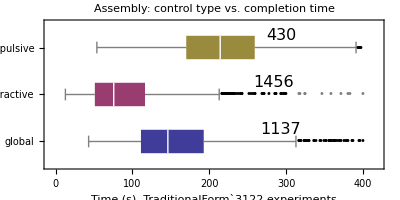

```mathematica
task = 2;
varyControl =GatherBy[Part[TaskData⟦task⟧,;;,2;;],First];
cleanControl=Table[DeleteCases[varyControl[[n,;;,3]],n_/;n>400] ,{n,1,Length[varyControl]}];
controlModes = varyControl⟦;;,1,1⟧;
BoxWhiskerChart[cleanControl,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{controlModes,Length/@cleanControl},{Axis,{.70,1}}],
AspectRatio->.5,
PlotLabel-> Style["Assembly: control type vs. completion time",FontSize->FontSz],
ChartStyle->1,ChartLabels->varyControl⟦;;,1,1⟧,BarOrigin->Left,LabelStyle->FontSz,FrameLabel->{StringForm[ "Time (s), `` experiments",Length[TaskData⟦task⟧]]}]
Export["../pictures/pdf/ResVaryControl.pdf",%];
```

### ANOVA Analysis (null hypothesis: the control type does not matter)

```mathematica
Needs["ANOVA`"]
ANOVA[Transpose[{Flatten[varyControl⟦;;,;;,1⟧],Flatten[varyControl⟦;;,;;,3⟧]}]]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 2 | 9.25299×10^6 | 4.62649×10^6 | 74.1783 | 3.36867×10^-32
Error | 3119 | 1.94532×10^8 | 62369.9 |  | 
Total | 3121 | 2.03785×10^8 |  |  | ,CellMeans→All | 154.61
Model[attractive] | 104.506
Model[global] | 175.409
Model[repulsive] | 257.465}